Particle distribution in scalar field

For a detailed derivation in the context of Gaussian lasers refer to: https://arxiv.org/abs/2106.01877

Notebook by: Óscar Amaro, June 2021 @ GoLP-EPP

Introduction
In this notebook we show how to obtain a particle distribution in a scalar field, both analytically and numerically. 
Given a particle density n(x) = dN/dx and a field ϕ(x), what is the fraction of particles that interact with ϕ=ϕ’?

One approach is to write dN/dϕ=(dN/dx)/(dϕ/dx) as a function of ϕ only.
For example, the particle density follows dN/dx = n(x) = exp(-α x^2) and the field is ϕ(x) = exp(-x^2).
Inverting the relation between coordinate and field x = Sqrt[-Log[ϕ]]
Thus |∂ϕ/∂x| = |-2 x ϕ| = 2 ϕ Sqrt[-Log[ϕ]]
Also n(x(ϕ)) = exp(-α (-Log[ϕ])) = ϕ^α
Finally dN/dϕ = ϕ^(α-1) / (2 Sqrt[-Log[ϕ]])

Another approach (numerical) might be to calculate the integral dN/dϕ(ϕ’) = ∫ δ(ϕ’-ϕ(x)) (dN/dx)(x) dx

Finally one can sample particle coordinates following  n(x) = exp(-α x^2), calculate the local ϕ(x) and build a histogram.

All three approaches can be generalized to higher dimensions.
Here we show that both give the same result for the previous example.

```mathematica
(* clear variables *)
Clear[x,ϕ,ϕx,n,α,xlim]
Clear[dNdϕ,nrm]
Clear[DOS,tabDOS]
Clear[Nsmpl,xsmpl,ϕsmpl,nbins,tabSMPL]
Clear[plt1,plt2,plt3]

(* particle density *)
n[x_]:=Exp[-α x^2]

(* scalar field *)
ϕx[x_]:=Exp[-x^2]

(* choose a specific α *)
α=0.5;
(* limit for numerical integration *)
xlim=100α;
```

Analytical approach

```mathematica
(* analytical distribution *)
dNdϕ=ϕ^(α-1)/(2Sqrt[-Log[ϕ]]);
(* normalize distribution *)
nrm=NIntegrate[dNdϕ,{ϕ,0,1}]//Quiet;
```

Numerical integration approach

```mathematica
(* numerical integration approach *)
DOS[ϕ_]:=Quiet[Integrate[DiracDelta[ϕ-ϕx[x]] n[x],{x,-xlim,+xlim}]]/Quiet[Integrate[ n[x],{x,-xlim,+xlim}]]
tabDOS=ParallelTable[{ϕ,DOS[ϕ]},{ϕ,0.0001,0.9999,0.05}];
```

Sampling approach

```mathematica
(* generate coordinates *)
Nsmpl = 100000;
xsmpl= RandomVariate[NormalDistribution[],{Nsmpl}]/Sqrt[2α];
ϕsmpl = ϕx[xsmpl];
Histogram[xsmpl];

(* histogram *)
nbins=100;
Histogram[xsmpl,50];
binsX=ParallelTable[ϕ,{ϕ,0,1,1/(nbins-1)}];
binsY=BinCounts[ϕsmpl,{0,1,1/nbins}];
tabSMPL=Transpose[{binsX,(binsY /Nsmpl)/(1/nbins)}];
```

Plot

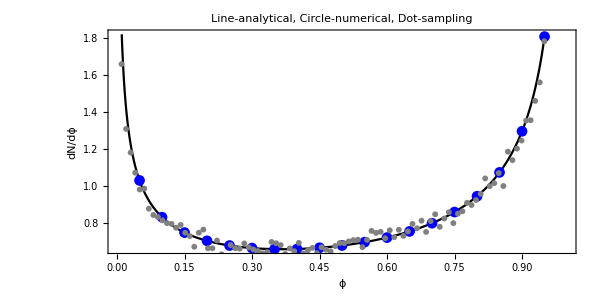

```mathematica
(* plot *)
plt1=Plot[dNdϕ/nrm,{ϕ,0,1},Frame->True,FrameStyle->Directive[20,Black],FrameLabel->{Text[Style["ϕ",20,Black]],Text[Style["dN/dϕ",20,Black]]},AspectRatio->1/2,ImageSize->600,PlotLabel->Text[Style["Line-analytical, Circle-numerical, Dot-sampling",20,Black]],PlotStyle->Black];
plt2=ListPlot[tabDOS,PlotStyle->Blue];
plt3=ListPlot[tabSMPL,Joined->False,PlotStyle->Directive[Gray,PointSize[0.007]]];
Show[{plt1,plt2,plt3}]
```